# Taggar/MGroups

Mathematica package that implements some parts of finite group theory

## Paclet Manifest

"Documentation"

"English"

"Guides"

"MGroupsPackage.nb"DocumentationEnglishGuidesMGroupsPackage.nb

"ReferencePages"

"Symbols"

"FormMAction.nb"DocumentationEnglishReferencePagesSymbolsFormMAction.nb

"FormMGroup.nb"DocumentationEnglishReferencePagesSymbolsFormMGroup.nb

"MAbelianQ.nb"DocumentationEnglishReferencePagesSymbolsMAbelianQ.nb

"MAction.nb"DocumentationEnglishReferencePagesSymbolsMAction.nb

"MAdditiveGroup.nb"DocumentationEnglishReferencePagesSymbolsMAdditiveGroup.nb

"MAutomorphism.nb"DocumentationEnglishReferencePagesSymbolsMAutomorphism.nb

"MCayleyGraph3D.nb"DocumentationEnglishReferencePagesSymbolsMCayleyGraph3D.nb

"MCayleyGraph.nb"DocumentationEnglishReferencePagesSymbolsMCayleyGraph.nb

"MCayleyTable.nb"DocumentationEnglishReferencePagesSymbolsMCayleyTable.nb

"MCoset.nb"DocumentationEnglishReferencePagesSymbolsMCoset.nb

"MCycleForm.nb"DocumentationEnglishReferencePagesSymbolsMCycleForm.nb

"MCyclicQ.nb"DocumentationEnglishReferencePagesSymbolsMCyclicQ.nb

"MDihedralGroup.nb"DocumentationEnglishReferencePagesSymbolsMDihedralGroup.nb

"MEDP.nb"DocumentationEnglishReferencePagesSymbolsMEDP.nb

"MElementCentralizer.nb"DocumentationEnglishReferencePagesSymbolsMElementCentralizer.nb

"MElementInverse.nb"DocumentationEnglishReferencePagesSymbolsMElementInverse.nb

"MElementOrbit.nb"DocumentationEnglishReferencePagesSymbolsMElementOrbit.nb

"MElementOrder.nb"DocumentationEnglishReferencePagesSymbolsMElementOrder.nb

"MElementPower.nb"DocumentationEnglishReferencePagesSymbolsMElementPower.nb

"MElementStabilizer.nb"DocumentationEnglishReferencePagesSymbolsMElementStabilizer.nb

"MFactorGroup.nb"DocumentationEnglishReferencePagesSymbolsMFactorGroup.nb

"MGenerateSubgroup.nb"DocumentationEnglishReferencePagesSymbolsMGenerateSubgroup.nb

"MGroupCenter.nb"DocumentationEnglishReferencePagesSymbolsMGroupCenter.nb

"MGroupDomain.nb"DocumentationEnglishReferencePagesSymbolsMGroupDomain.nb

"MGroupIdentity.nb"DocumentationEnglishReferencePagesSymbolsMGroupIdentity.nb

"MGroup.nb"DocumentationEnglishReferencePagesSymbolsMGroup.nb

"MGroupOrder.nb"DocumentationEnglishReferencePagesSymbolsMGroupOrder.nb

"MHomomorphism.nb"DocumentationEnglishReferencePagesSymbolsMHomomorphism.nb

"MInnerAutomorphism.nb"DocumentationEnglishReferencePagesSymbolsMInnerAutomorphism.nb

"MInversesTable.nb"DocumentationEnglishReferencePagesSymbolsMInversesTable.nb

"MIsomorphism.nb"DocumentationEnglishReferencePagesSymbolsMIsomorphism.nb

"MKernelAction.nb"DocumentationEnglishReferencePagesSymbolsMKernelAction.nb

"MKlein4Group.nb"DocumentationEnglishReferencePagesSymbolsMKlein4Group.nb

"MMorphismKernel.nb"DocumentationEnglishReferencePagesSymbolsMMorphismKernel.nb

"MMultiplicativeGroup.nb"DocumentationEnglishReferencePagesSymbolsMMultiplicativeGroup.nb

"MNormalSubgroupQ.nb"DocumentationEnglishReferencePagesSymbolsMNormalSubgroupQ.nb

"MNormalSubgroups.nb"DocumentationEnglishReferencePagesSymbolsMNormalSubgroups.nb

"MonoidQ.nb"DocumentationEnglishReferencePagesSymbolsMonoidQ.nb

"MPermutationRepresentation.nb"DocumentationEnglishReferencePagesSymbolsMPermutationRepresentation.nb

"MPermutationsGroup.nb"DocumentationEnglishReferencePagesSymbolsMPermutationsGroup.nb

"MQuaternionGroup.nb"DocumentationEnglishReferencePagesSymbolsMQuaternionGroup.nb

"MSubgroupLattice3D.nb"DocumentationEnglishReferencePagesSymbolsMSubgroupLattice3D.nb

"MSubgroupLattice.nb"DocumentationEnglishReferencePagesSymbolsMSubgroupLattice.nb

"MSubgroupQ.nb"DocumentationEnglishReferencePagesSymbolsMSubgroupQ.nb

"MSubgroups.nb"DocumentationEnglishReferencePagesSymbolsMSubgroups.nb

"MTuple.nb"DocumentationEnglishReferencePagesSymbolsMTuple.nb

"MVisualiseMorphism.nb"DocumentationEnglishReferencePagesSymbolsMVisualiseMorphism.nb

"SemiGroupQ.nb"DocumentationEnglishReferencePagesSymbolsSemiGroupQ.nb

"Tutorials"

"Kernel"

"MGroups.wl"KernelMGroups.wl

"LICENSE"LICENSE

"PacletInfo.wl"PacletInfo.wl

"README.md"README.md

"ResourceDefinition.nb"ResourceDefinition.nb

"Tests"

"TestBasic.nb"TestsTestBasic.nb

"TestBasic.wlt"TestsTestBasic.wlt

"TestSubgroups.nb"TestsTestSubgroups.nb

"TestSubgroups.wlt"TestsTestSubgroups.wlt

## Web Content

### Headline Image

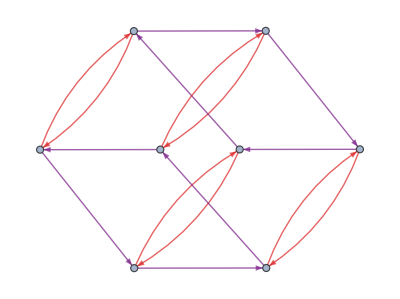

### Basic Description

MGroups is a mathematica package that implements a part of finite group theory. It offers a user-friendly interface for performing a range of computations involving finite groups including Z_n, U_n, D_n, S_n, and more. The package allows users to define and analyse groups through Cayley tables and provides functionality for investigating group operations, subgroup structures (lattices), group morphisms, and more.
 Each group is defined in terms of its Cayley table representation itself, and operations are applied appropriately.

Computational tools play a vital role in modern mathematics by automating complex and often tedious calculations, thereby freeing users from manual labour and enabling deeper exploration of abstract concepts. In that essence, MGroups is designed primarily for undergraduate students beginning with group theory, as well as for educators seeking a user-friendly tool to demonstrate group-theoretic concepts interactively.

### Details

Additional information about the paclet.

### Primary Context

Taggar`MGroups`

### Main Guide Page

## Examples

### Initialization for Examples

```mathematica
PacletDirectoryLoad[NotebookDirectory[]];
```

```mathematica
Needs["Taggar`MGroups`"];
```

### Basic Examples

Define a group using the FormGroup command:

```mathematica
d:={0,1,2,3,4}
f[x_,y_]:=Mod[x+y,5]
G=Taggar`MGroups`FormMGroup[d,f]
```

MGroup[…]

Click on the + icon to see that the identity for this group is 0. See for example its table of inverses:

```mathematica
MInversesTable[G]
```

x | x^-1 | |x|=|x^-1|
0 | 0 | 1
1 | 4 | 5
2 | 3 | 5
3 | 2 | 5
4 | 1 | 5

Define a group using one of the available commands:

```mathematica
Subscript[d, 4]=Taggar`MGroups`MDihedralGroup[4]
```

MGroup[…]

Then study it using the available commands, for example see its Cayley table:

```mathematica
Taggar`MGroups`MCayleyTable[Subscript[d, 4]]
```

| e | r^1 | r^2 | r^3 | s | r^1s | r^2s | r^3s
e | e | r^1 | r^2 | r^3 | s | r^1s | r^2s | r^3s
r^1 | r^1 | r^2 | r^3 | e | r^3s | s | r^1s | r^2s
r^2 | r^2 | r^3 | e | r^1 | r^2s | r^3s | s | r^1s
r^3 | r^3 | e | r^1 | r^2 | r^1s | r^2s | r^3s | s
s | s | r^1s | r^2s | r^3s | e | r^1 | r^2 | r^3
r^1s | r^1s | r^2s | r^3s | s | r^3 | e | r^1 | r^2
r^2s | r^2s | r^3s | s | r^1s | r^2 | r^3 | e | r^1
r^3s | r^3s | s | r^1s | r^2s | r^1 | r^2 | r^3 | e

or its Cayley graph using the generators {r,s}:

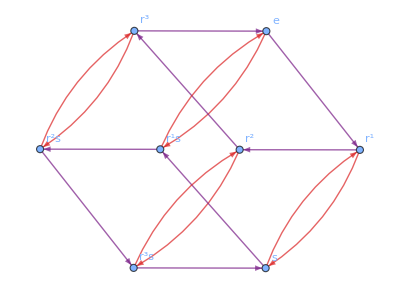

```mathematica
Taggar`MGroups`MCayleyGraph[Subscript[d, 4],{Taggar`MGroups`MSymmetry[0,1],Taggar`MGroups`MSymmetry[1,1]}]
```

See its subgroups:

```mathematica
Taggar`MGroups`MSubgroups[Subscript[d, 4]]
```

Subgroup | Generated by
{e} | {e}
{e,r^1,r^2,r^3} | {r^1}
{e,r^2} | {r^2}
{e,s} | {s}
{e,r^1s} | {r^1s}
{e,r^2s} | {r^2s}
{e,r^3s} | {r^3s}
{e,r^1,r^2,r^3,s,r^1s,r^2s,r^3s} | {r^1,s}
{e,r^2,s,r^2s} | {r^2,s}
{e,r^2,r^1s,r^3s} | {r^2,r^1s}

### Scope

The package also allows drawing subgroup lattices (highlighting normal subgroups):

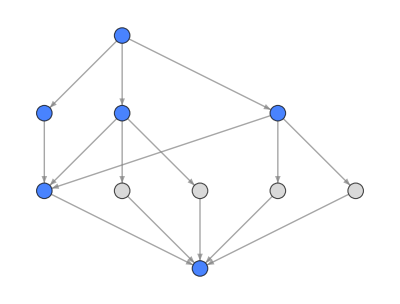

```mathematica
Taggar`MGroups`MSubgroupLattice[Subscript[d, 4],MHighlight->MNormalSubgroupQ]
```

See the same lattice in 3D with layers:

```mathematica
Taggar`MGroups`MSubgroupLattice3D[Subscript[d, 4]]
```

-Graphics3D-

More complex example: the group of permutations on 4 symbols:

```mathematica
Subscript[S, 4]=Taggar`MGroups`MPermutationsGroup[4]
```

MGroup[…]

its subgroup lattice:

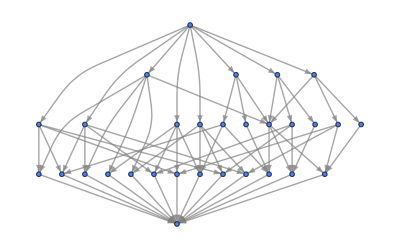

```mathematica
Taggar`MGroups`MSubgroupLattice[Subscript[S, 4]]
```

and its Cayley graph in 3-D using the well-known generators (12) and (234):

```mathematica
Taggar`MGroups`MCayleyGraph3D[Subscript[S, 4],{Cycles[{{1,2}}],Cycles[{{2,3,4}}]}]
```

-Graphics3D-

## Source & Additional Information

### Creator

Naman Taggar <namtgr@gmail.com>

### Source Control Repository

https://github.com/zplus11/MGroups

### License

MIT License [»](https://resources.wolframcloud.com/PacletRepository/licenses/MIT)
 Apache License 2.0 [»](https://resources.wolframcloud.com/PacletRepository/licenses/Apache-2.0)
 Creative Commons Zero v1.0 Universal [»](https://resources.wolframcloud.com/PacletRepository/licenses/CC0-1.0)
 NoneA license is not required for personal deployments

### Keywords

group theory

finite groups

abstract algebra

discrete algebra

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Machine Learning
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Original Source References and Attributions

Source, reference or citation

### Links

Link to other related material

### Compatibility

#### Wolfram Language Version

12.3+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

### Disclosures

Local filesDisclosuresLocalFilesChoose this option if your paclet directly does any of the following during loading or normal usage:
◼ Creates, deletes or modifies local files
◼ Imports data from local files
File operations related to normal paclet installation and loading are excepted.Click for more information

Wolfram accountDisclosuresWolframAccountChoose this option if your paclet directly does any of the following:
◼ Requires, uses, or records any information related to user’s Wolfram ID
◼ Interacts with the user’s Cloud account or Wolfram account
◼ Creates, deletes or modifies the user’s cloud objects
◼ Creates or executes cloud deployed scheduled tasks
◼ Uses cloud credits, service credits or Wolfram credits
◼ Makes WolframAlpha callsClick for more information

External servicesDisclosuresExternalServicesChoose this option if your paclet directly does any of the following:
◼ Makes requests to external services (http, ftp, ssh, etc)
◼ Creates or uses service connection
◼ Send emailsClick for more information

Wolfram Language system configurationDisclosuresWLSystemConfigurationChoose this option if your paclet directly does any of the following:
◼ Creates persistent local scheduled tasks
◼ Modifies WL system or environment settings
◼ Modifies $Path, Directory, or similar
◼ Installs additional paclets or dependencies
◼ Creates or imports non-public ResourceObject content
◼ Makes FrontEnd modifications
◼ Internal handlersClick for more information

Wolfram Language built-in symbolsDisclosuresWLSystemSymbolsChoose this option if your paclet directly modifies definitions of built-in symbols such as those in System` or other internal contexts.Click for more information

Paclet dependenciesDisclosuresPacletDependenciesChoose this option if your paclet directly installs or updates any additional paclets. Paclets that are included with the Wolfram system do not require a disclosure.Click for more information

OS configurationDisclosuresOSConfigurationChoose this option if your paclet directly does any of the following:
◼ Modifies OS settings
◼ Makes any use of SystemCredentialClick for more information

Local system interactionsDisclosuresLocalSystemInteractionsChoose this option if your paclet directly does any of the following:
◼ Executes Shell or RUN commands
◼ Uses external evaluators via ExternalEvaluate
◼ Interacts with external libraries
◼ Reads or writes to streams or sockets
◼ Launches parallel kernels, subkernels or GPUsClick for more information

OtherDisclosuresOtherAdd additional text as needed in a new cell below to document any additional disclosures that are not listed above.Click for more information

## Author Notes

Additional information about limitations, issues, etc.